```mathematica
f[x_,mu_,s_]:=(*1/(s √(2π))*)Exp[(- 1)/2((x-mu)/s)^2]
```

```mathematica
g[x_,r_]:=(1+r)/(1+r x)^2
```

```mathematica
h[x_,mu_,s_]:=Exp[- ((x-mu)/s)]
```

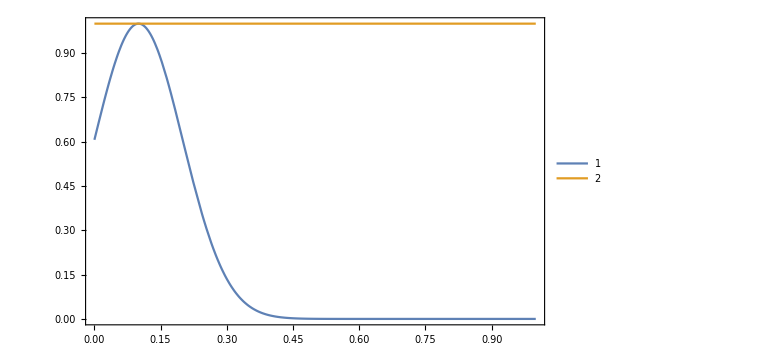

```mathematica
Plot[{f[x,0.1,0.1],f[x,0.1,1000]},{x,10^-5,1},Frame->True,ImageSize->Large,PlotLegends->Automatic]
```

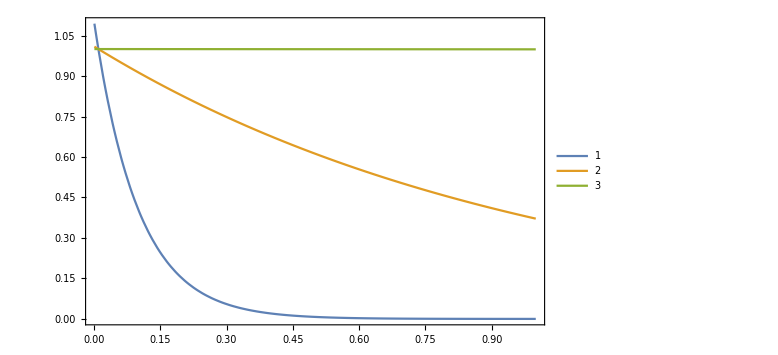

```mathematica
Plot[{h[x,10^-2,0.1],h[x,10^-2,1],h[x,10^-2,1000]},{x,10^-3,1},Frame->True,ImageSize->Large,PlotLegends->Automatic]
```

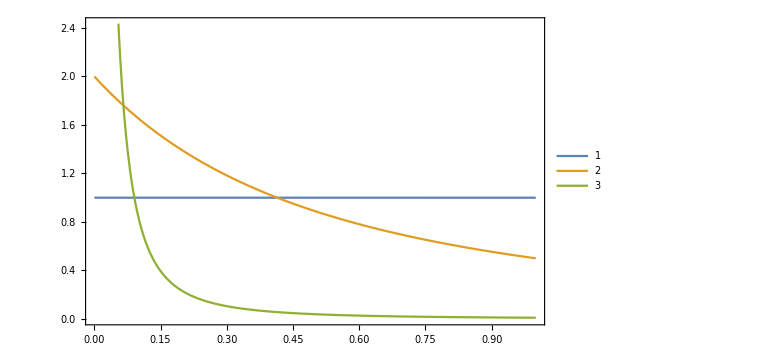

```mathematica
Plot[{g[x,0.0001],g[x,1],g[x,100]},{x,10^-6,1},Frame->True,ImageSize->Large,PlotLegends->Automatic]
```

```mathematica
ve=1000;(*km/sec*)
u=100;
w=(ve^2+u^2)^0.5;
```

```mathematica
eps=0.99;
```

```mathematica
G4[r_]:=NIntegrate[g[x1,r]g[x2,r]g[x3,r]g[x4,r]HeavisideTheta[ve-w ((1-x1)(1-x2)(1-x3)(1-x4))^0.5],{x1,0,eps},{x2,0,eps},{x3,0,eps},{x4,0,eps},WorkingPrecision->10,PrecisionGoal->2]
```

```mathematica
G4[0.0001]
```

0.960599852

```mathematica
G3[r_]:=NIntegrate[g[x1,r]g[x2,r]g[x3,r]HeavisideTheta[ve-w ((1-x1)(1-x2)(1-x3))^0.5],{x1,0,eps},{x2,0,eps},{x3,0,eps},WorkingPrecision->10,PrecisionGoal->2]
```

```mathematica
G3[0.1]
```

0.9729500887